```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*ExpIntegralE[k+1,k*A*(d-1)],d->1,Assumptions->{k>3/2,A>0}]
Limit[k*Exp[k*A*(d-1)]ExpIntegralE[k+1,k*A*(d-1)],d->Infinity,Assumptions->{k>3/2,A>0}]
```

1

0

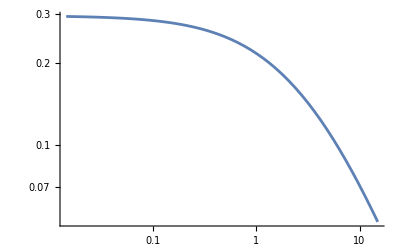

0.0521897

0.0472444

0.0526956

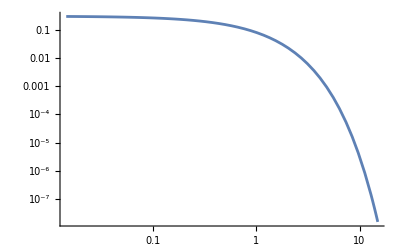

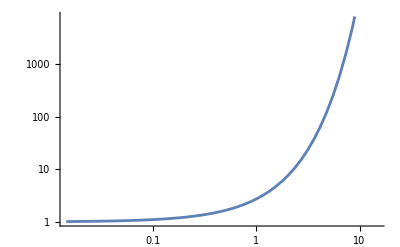

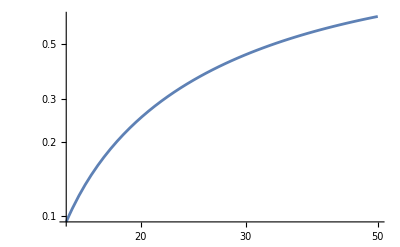

```mathematica
LogLogPlot[Exp[x]*ExpIntegralE[3.37+1,x],{x,0,15}]
Exp[15]*ExpIntegralE[3.37+1,15]
g2[x_,κ_]=1/x+(-1-κ)/x^2;
g5[x_,κ_]=1/x+(-1-κ) (1/x)^2+(1+κ) (2+κ) (1/x)^3-(1+κ) (2+κ) (3+κ) (1/x)^4+(1+κ) (2+κ) (3+κ) (4+κ) (1/x)^5;
g2[15,3.37]
g5[15,3.37]
LogLogPlot[ExpIntegralE[3.37+1,x],{x,0,15}]
LogLogPlot[Exp[x],{x,0,15}]

LogLogPlot[(Exp[15]*ExpIntegralE[3.37+1,15] - g2[x,3.37])/(Exp[15]*ExpIntegralE[3.37+1,15]),{x,15,50}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->Infinity,Assumptions->{k>3/2}]
FullSimplify[Series[κ*Exp[1/y]*ExpIntegralE[κ+1,1/y],{y,0,2},Assumptions->κ>3/2],{κ>3/2,y∈Reals}]

FullSimplify[Series[Exp[1/y]*ExpIntegralE[κ+1,1/y],{y,0,2},Assumptions->κ>3/2],{κ>3/2,y∈Reals}]
```

0

κ y-κ (1+κ) y^2+O[y]^3

y+(-1-κ) y^2+O[y]^3

```mathematica
y=1/x;
κ y-κ (1+κ) y^2
```

κ/x-(κ (1+κ))/x^2

1543.46

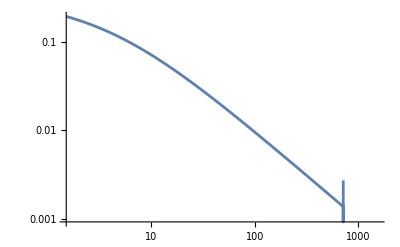

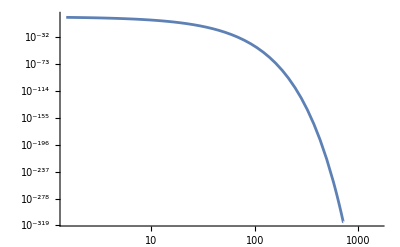

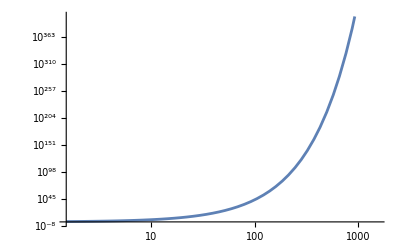

```mathematica
xf=458*3.37
LogLogPlot[Exp[x]*ExpIntegralE[3.37+1,x],{x,0,xf}]
LogLogPlot[ExpIntegralE[3.37+1,x],{x,0,xf}]
LogLogPlot[Exp[x],{x,0,xf}]
```

```mathematica
(1/15.)^4
```

0.0000197531

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*ExpIntegralE[k+1,k*A*(d-1)],d->1,Assumptions->{k>3/2,A>0}]
Limit[k*Exp[k*A*(d-1)]ExpIntegralE[k+1,k*A*(d-1)],d->Infinity,Assumptions->{k>3/2,A>0}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->0,Assumptions->{k>2/2}]
FullSimplify[Series[κ*Exp[x]*ExpIntegralE[κ+1,x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]

FullSimplify[Series[Exp[x]*ExpIntegralE[κ+1,x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]
```

1

(1+x/(1-κ)+x^2/(2-3 κ+κ^2)+O[x]^3)+x^κ (κ Gamma[-κ]+κ Gamma[-κ] x+1/2 κ Gamma[-κ] x^2+O[x]^3)

(1/κ+x/(κ-κ^2)+x^2/(2 κ-3 κ^2+κ^3)+O[x]^3)+x^κ (Gamma[-κ]+Gamma[-κ] x+1/2 Gamma[-κ] x^2+O[x]^3)

```mathematica
Plot[{(1+x/(1-κ)+x^2/(2-3 κ+κ^2))/(κ*Exp[x]*ExpIntegralE[κ+1,x]),},{x,0,2},PlotLegends->"Expressions",Frame->True,FrameLabel->{"x","approx"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Series[κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]
FullSimplify[Series[κ*Exp[x]*ExpIntegralE[κ+1,x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]
```

(1-(κ x)/(-1+κ)+(κ^2 x^2)/(2-3 κ+κ^2)+O[x]^3)+x^κ (κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] x+1/2 κ^(3+κ) Gamma[-κ] x^2+O[x]^3)

(1+x/(1-κ)+x^2/(2-3 κ+κ^2)+O[x]^3)+x^κ (κ Gamma[-κ]+κ Gamma[-κ] x+1/2 κ Gamma[-κ] x^2+O[x]^3)

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: 0.0100018^300. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0118386^300. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0136753^300. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

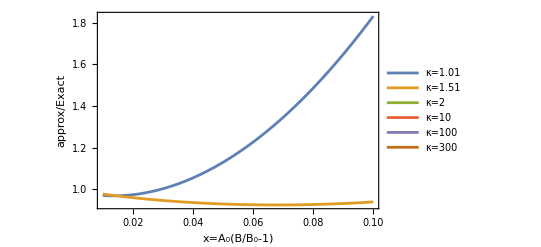

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;
(*κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]*)
f1st[x_,κ_]:=1-(κ x)/(-1+κ)+x^κ *(κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] x);


f2nd[x_,κ_]:=1-(κ x)/(-1+κ)+(κ^2 x^2)/(2-3 κ+κ^2)+x^κ *(κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] x+1/2 κ^(3+κ) Gamma[-κ] x^2);
f[x_,κ_]:=f1st[x,κ];

Plot[{f[x,κ0],f[x,κ1],f[x,κ2],f[x,κ3],f[x,κ4],f[x,κ5]},{x,0.01,0.1},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=A_0(B/B_0-1)","approx/Exact"}]
```

```mathematica
f1[x_,κ_]:=κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]
Plot[{f1[x,κ0],f1[x,κ1],f1[x,κ2],f1[x,κ3],f1[x,κ4]},{x,0.01,0.9},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100"},Frame->True,FrameLabel->{"x=A_0(B/B_0-1)","Exact"}]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->Infinity,Assumptions->{k>3/2}]
FullSimplify[Series[κ*Exp[1/y]*ExpIntegralE[κ+1,1/y],{y,0,3},Assumptions->κ>3/2],{κ>3/2,y∈Reals}]
```

0

κ y-κ (1+κ) y^2+κ (1+κ) (2+κ) y^3+O[y]^4

ⅇ^(x κ) κ ExpIntegralE[1+κ,x κ]

General::munfl: Exp[-1121.5] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: Exp[-1158.05] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: Exp[-1194.27] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

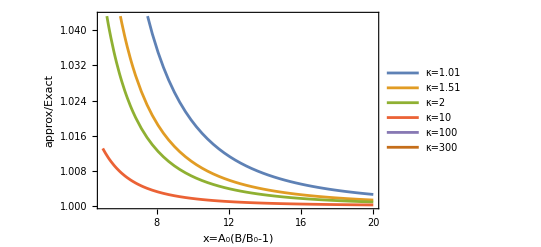

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;
κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]

f[x_,κ_]:=(1/x-((1+κ) 1/x^2)/κ+((1+κ) (2+κ) 1/x^3)/κ^2)/(κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]);

Plot[{f[x,κ0],f[x,κ1],f[x,κ2],f[x,κ3],f[x,κ4],f[x,κ5]},{x,5,20},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=A_0(B/B_0-1)","approx/Exact"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->Infinity,Assumptions->{k>2/2}]
FullSimplify[Series[κ*Exp[κ/y]*ExpIntegralE[κ+1,κ/y],{y,0,3},Assumptions->κ>2/2],{κ>2/2,y∈Reals}]
```

0

y-((1+κ) y^2)/κ+((1+κ) (2+κ) y^3)/κ^2+O[y]^4

General::munfl: Exp[-827.417] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: Exp[-829.553] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: Exp[-831.675] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

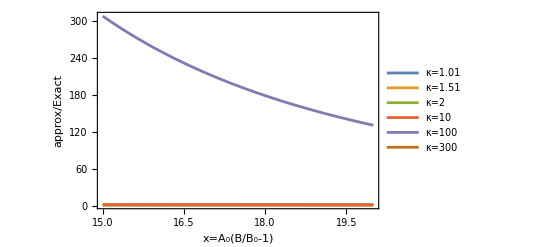

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

f[x_,κ_]:=(κ 1/x-κ (1+κ) 1/x^2+κ (1+κ) (2+κ) 1/x^3)/(κ*Exp[x]*ExpIntegralE[κ+1,x]);

Plot[{f[x,κ0],f[x,κ1],f[x,κ2],f[x,κ3],f[x,κ4],f[x,κ5]},{x,15,20},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=A_0(B/B_0-1)","approx/Exact"},PlotRange->All]
```

Remove::rmnsm: There are no symbols matching "Global`*".

General::munfl: -7.98783/(3.06057512216×10^614) is too small to represent as a normalized machine number; precision may be lost.

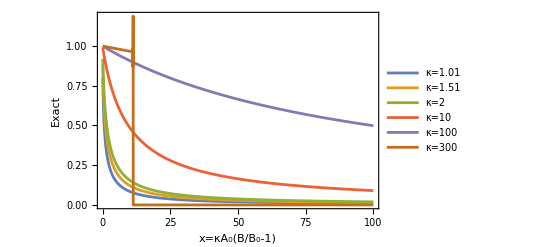

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;
f1[x_,κ_]:=κ*Exp[x]*ExpIntegralE[κ+1,x]
Plot[{f1[x,κ0],f1[x,κ1],f1[x,κ2],f1[x,κ3],f1[x,κ4],f1[x,κ5]},{x,0.1,100},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Exact"}]
```

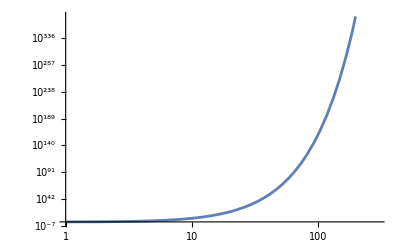

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
LogLogPlot[Gamma[κ+1],{κ,1.01,300}]
```

General::munfl: -7.6034/(7.886578673648×10^374) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.91025/(7.886578673648×10^374) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.50479/(7.886578673648×10^374) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

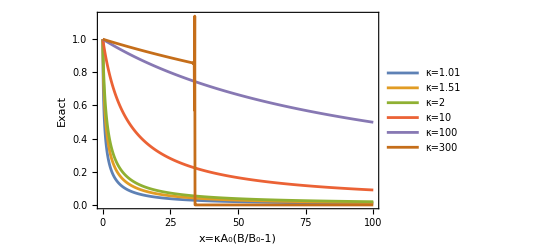

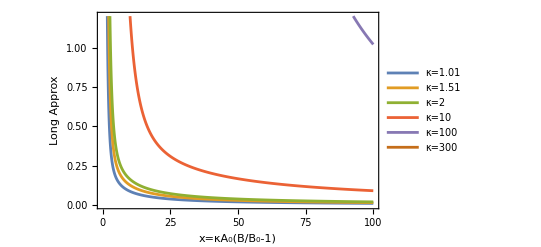

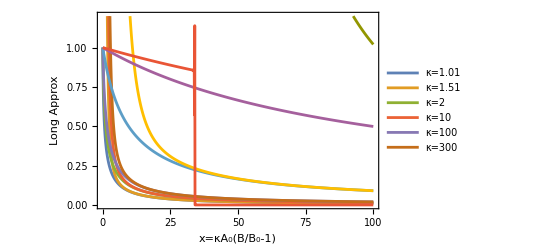

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=200.;
f1[x_,κ_]:=κ*Exp[x]*ExpIntegralE[κ+1,x]
f2[x_,κ_]:=κ/x-κ (1+κ)/x^2+κ (1+κ) (2+κ)/x^3;
list0=Table[{x,f1[x,κ0]},{x,0,100,0.1}];
list1=Table[{x,f1[x,κ1]},{x,0,100,0.1}];
list2=Table[{x,f1[x,κ2]},{x,0,100,0.1}];
list3=Table[{x,f1[x,κ3]},{x,0,100,0.1}];
list4=Table[{x,f1[x,κ4]},{x,0,100,0.1}];
list5=Table[{x,f1[x,κ5]},{x,0,100,0.1}];

listt0=Table[{x,f2[x,κ0]},{x,0,100,0.1}];
listt1=Table[{x,f2[x,κ1]},{x,0,100,0.1}];
listt2=Table[{x,f2[x,κ2]},{x,0,100,0.1}];
listt3=Table[{x,f2[x,κ3]},{x,0,100,0.1}];
listt4=Table[{x,f2[x,κ4]},{x,0,100,0.1}];
listt5=Table[{x,f2[x,κ5]},{x,0,100,0.1}];

ListPlot[{list0,list1,list2,list3,list4,list5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Exact"},Joined->True]
ListPlot[{listt0,listt1,listt2,listt3,listt4,listt5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Long Approx"},PlotRange->{All,{0,1.2}},Joined->True]

ListPlot[{list0,listt0,list1,listt1,list2,listt2,list3,listt3,list4,listt4,list5,listt5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Long Approx"},PlotRange->{All,{0,1.2}},Joined->True]
```

General::munfl: Exp[-709.042] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.059] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.076] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-714.702] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.832] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-744.711] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-777.776] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-878.869] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-956.405] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Part::partd: Part specification {{0.,1.},{0.1,0.799753},{0.2,0.702569},{0.3,0.634417},{0.4,0.581969},«41»,{4.6,0.157675},{4.7,0.155148},{4.8,0.152703},{4.9,0.150335},«951»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,5741.88},{0.2,696.609},{0.3,200.884},{0.4,82.732},{0.5,41.4867},«40»,{4.6,0.184273},{4.7,0.1798},{4.8,0.175586},{4.9,0.171607},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0.,1.},{0.1,0.799753},{0.2,0.702569},{0.3,0.634417},{0.4,0.581969},«41»,{4.6,0.157675},{4.7,0.155148},{4.8,0.152703},{4.9,0.150335},«951»}⟦0,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{0.,1.},{0.1,0.840245},{0.2,0.745441},{0.3,0.675862},{0.4,0.62107},{0.5,0.576161},«40»,{4.6,0.163675},{4.7,0.160983},{4.8,0.158379},{4.9,0.15586},«951»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,3707.68},{0.2,446.432},{0.3,127.972},{0.4,52.4845},{0.5,26.2623},«40»,{4.6,0.178532},{4.7,0.174733},{4.8,0.171125},{4.9,0.167693},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0.,1.},{0.1,0.840245},{0.2,0.745441},{0.3,0.675862},{0.4,0.62107},{0.5,0.576161},«40»,{4.6,0.163675},{4.7,0.160983},{4.8,0.158379},{4.9,0.15586},«951»}⟦0,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{0.,1.},{0.1,0.859734},{0.2,0.767652},{0.3,0.698056},{0.4,0.642397},{0.5,0.596347},«40»,{4.6,0.166936},{4.7,0.164151},{4.8,0.161458},{4.9,0.158854},«951»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,2860.},{0.2,342.5},{0.3,97.7778},{0.4,40.},{0.5,20.},«40»,{4.6,0.177324},{4.7,0.173757},{4.8,0.170356},{4.9,0.167107},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0.,1.},{0.1,0.859734},{0.2,0.767652},{0.3,0.698056},{0.4,0.642397},{0.5,0.596347},«40»,{4.6,0.166936},{4.7,0.164151},{4.8,0.161458},{4.9,0.158854},«951»}⟦0,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {{0.,1.},{0.1,0.901071},{0.2,0.821302},{0.3,0.755296},{0.4,0.699606},{0.5,0.651893},«40»,{4.6,0.176018},{4.7,0.172964},{4.8,0.170014},{4.9,0.167164},«951»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,1220.},{0.2,142.5},{0.3,40.},{0.4,16.25},{0.5,8.16},«40»,{4.6,0.178968},{4.7,0.175684},{4.8,0.172526},{4.9,0.169487},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0.,1.},{0.1,0.901071},{0.2,0.821302},{0.3,0.755296},{0.4,0.699606},{0.5,0.651893},«40»,{4.6,0.176018},{4.7,0.172964},{4.8,0.170014},{4.9,0.167164},«951»}⟦0,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Part::partd: Part specification {{0.,1.},{0.1,0.908335},{0.2,0.832171},{0.3,0.767862},{0.4,0.712827},{0.5,0.665185},{0.6,0.623536},«37»,{4.4,0.},{4.5,0.},{4.6,0.},{4.7,0.},{4.8,0.},{4.9,0.},«951»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,939.2},{0.2,108.525},{0.3,30.2667},{0.4,12.2844},{0.5,6.2016},«40»,{4.6,0.180244},{4.7,0.176967},{4.8,0.173812},{4.9,0.170772},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0.,1.},{0.1,0.908335},{0.2,0.832171},{0.3,0.767862},{0.4,0.712827},{0.5,0.665185},{0.6,0.623536},«37»,{4.4,0.},{4.5,0.},{4.6,0.},{4.7,0.},{4.8,0.},{4.9,0.},«951»}⟦0,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

Part::partd: Part specification {{0.,Indeterminate},{0.1,924.55},{0.2,106.756},{0.3,29.7611},{0.4,12.0789},{0.5,6.1004},«40»,{4.6,0.180324},{4.7,0.177047},{4.8,0.173892},{4.9,0.170852},«951»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

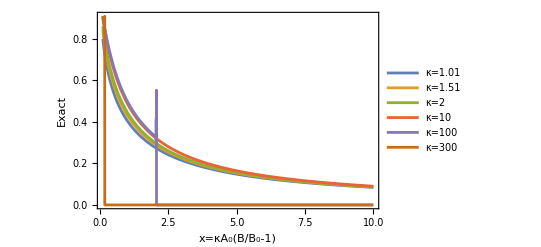

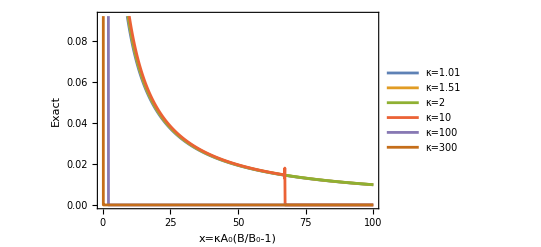

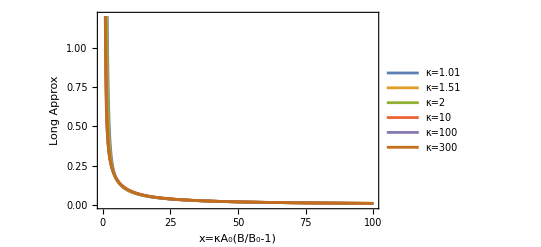

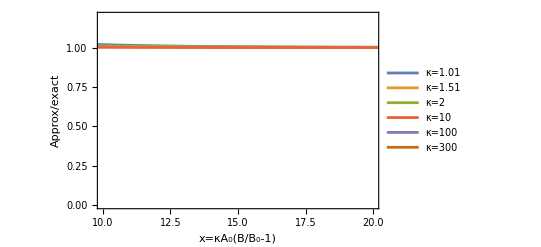

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=200.;
f1[x_,κ_]:=κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]
f2[x_,κ_]:=1/x-((1+κ) 1/x^2)/κ+((1+κ) (2+κ) 1/x^3)/κ^2;
list0=Table[{x,f1[x,κ0]},{x,0,100,0.1}];
list1=Table[{x,f1[x,κ1]},{x,0,100,0.1}];
list2=Table[{x,f1[x,κ2]},{x,0,100,0.1}];
list3=Table[{x,f1[x,κ3]},{x,0,100,0.1}];
list4=Table[{x,f1[x,κ4]},{x,0,100,0.1}];
list5=Table[{x,f1[x,κ5]},{x,0,100,0.1}];

listt0=Table[{x,f2[x,κ0]},{x,0,100,0.1}];
listt1=Table[{x,f2[x,κ1]},{x,0,100,0.1}];
listt2=Table[{x,f2[x,κ2]},{x,0,100,0.1}];
listt3=Table[{x,f2[x,κ3]},{x,0,100,0.1}];
listt4=Table[{x,f2[x,κ4]},{x,0,100,0.1}];
listt5=Table[{x,f2[x,κ5]},{x,0,100,0.1}];

listtt0=Table[{list0[[i,1]],listt0[[i,2]]/list0[[i,2]]},{i,0,Length[list0[[All,2]]]}];
listtt1=Table[{list1[[i,1]],listt1[[i,2]]/list1[[i,2]]},{i,0,Length[list0[[All,2]]]}];
listtt2=Table[{list2[[i,1]],listt2[[i,2]]/list2[[i,2]]},{i,0,Length[list0[[All,2]]]}];
listtt3=Table[{list3[[i,1]],listt3[[i,2]]/list3[[i,2]]},{i,0,Length[list0[[All,2]]]}];
listtt4=Table[{list4[[i,1]],listt4[[i,2]]/list4[[i,2]]},{i,0,Length[list0[[All,2]]]}];
listtt5=Table[{list5[[i,1]],listt5[[i,2]]/list5[[i,2]]},{i,0,Length[list0[[All,2]]]}];


Plot[{f1[x,κ0],f1[x,κ1],f1[x,κ2],f1[x,κ3],f1[x,κ4],f1[x,κ5]},{x,0.1,10},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Exact"}]
ListPlot[{list0,list1,list2,list3,list4,list5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Exact"},Joined->True]
ListPlot[{listt0,listt1,listt2,listt3,listt4,listt5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Long Approx"},PlotRange->{All,{0,1.2}},Joined->True]

ListPlot[{listtt0,listtt1,listtt2,listtt3,listtt4,listtt5},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"x=κA_0(B/B_0-1)","Approx/exact"},PlotRange->{{10,20},{0,1.2}},Joined->True]
```

```mathematica
Dimensions[list0]
list0[[x,2]]
```

{1001,2}

{0.,1.}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*1/η = κ, x= Subscript[A, 0]*(B/Subscript[B, 0]-1)*)
Series[Exp[x/η]/η*ExpIntegralE[1/η+1,x/η],{η,0,1},Assumptions->x>=0]
```

ⅇ^(x/η+O[η]^2) ExpIntegralE[1+1/η,x/η] (1/η+O[η]^2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

AsymptoticSolve[y==κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x],y,{κ,Infinity,3},Assumptions->x>=0]
```

AsymptoticSolve[y==ⅇ^(x κ) κ ExpIntegralE[1+κ,x κ],y,{κ,∞,3},Assumptions→x≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*1/η = κ, x= κ*Subscript[A, 0]*(B/Subscript[B, 0]-1)*)
Series[ExpIntegralE[1/η+1,x],{η,0,1},Assumptions->x>=0]
AsymptoticSolve[y==ExpIntegralE[κ+1,x],y,{κ,Infinity,1},Assumptions->x>=0]
```

ExpIntegralE[1+1/η,x]

AsymptoticSolve[y==ExpIntegralE[1+κ,x],y,{κ,∞,1},Assumptions→x≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*1/η = κ, x= κ*Subscript[A, 0]*(B/Subscript[B, 0]-1)*)
Series[(1+1/η)/(1/η*z),{η,0,10},Assumptions->z>=0]
```

1/z+η/z+O[η]^11

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*1/η = κ, x= κ*Subscript[A, 0]*(B/Subscript[B, 0]-1)*)
Series[Exp[-(κ*z)*t-(κ+1)*Log[t]],{t,1,1},Assumptions->{z>=0,κ>1}]
```

ⅇ^(-z κ)-ⅇ^(-z κ) (1+κ+z κ) (t-1)+O[t-1]^2

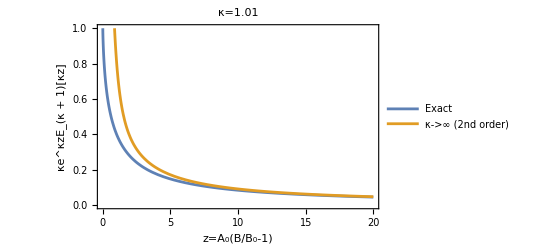

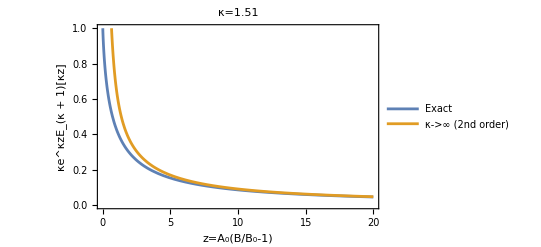

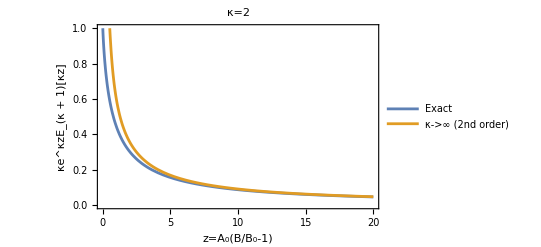

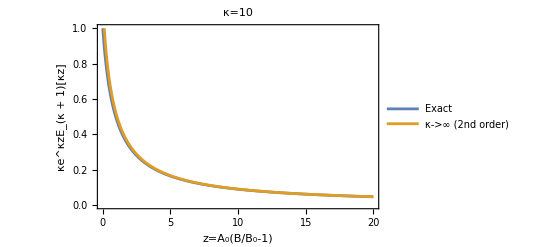

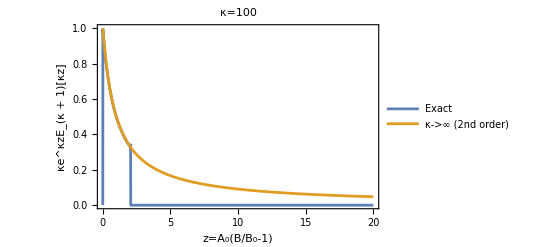

General::munfl: -7.80451/(3.06057512216×10^614) is too small to represent as a normalized machine number; precision may be lost.

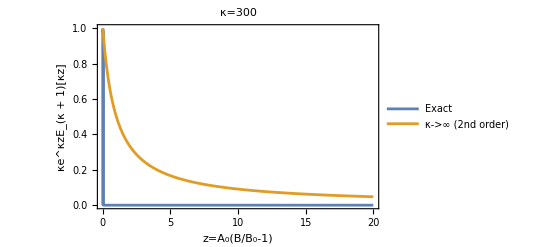

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

f[z_,κ_]:=κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z];
fa[z_,κ_]:=1/(1+z)+1/((1+z)^3*κ)+3/((1+z)^5*κ^2)+15/((1+z)^7*κ^3);
(*
Plot[{f[z,κ0],f[z,κ1],f[z,κ2],f[z,κ3],f[z,κ4],f[z,κ5]},{z,0,20},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Exact"},PlotRange->{All,{0,1}}]
Plot[{fa[z,κ0],fa[z,κ1],fa[z,κ2],fa[z,κ3],fa[z,κ4],fa[z,κ5]},{z,0,20},PlotLegends->{"κ=1.01","κ=1.51","κ=2","κ=10","κ=100","κ=300"},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Large κ Approx 2nd order"},PlotRange->{All,{0,1}}]*)

zmin = 0;
zmax = 20;
p0=Plot[{f[z,κ0],fa[z,κ0]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=1.01",PlotLegends->{"Exact","κ->∞ (2nd order)"}]
p1=Plot[{f[z,κ1],fa[z,κ1]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=1.51",PlotLegends->{"Exact","κ->∞ (2nd order)"}]

p2=Plot[{f[z,κ2],fa[z,κ2]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=2",PlotLegends->{"Exact","κ->∞ (2nd order)"}]

p3=Plot[{f[z,κ3],fa[z,κ3]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=10",PlotLegends->{"Exact","κ->∞ (2nd order)"}]

p4=Plot[{f[z,κ4],fa[z,κ4]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=100",PlotLegends->{"Exact","κ->∞ (2nd order)"}]
p5=Plot[{f[z,κ5],fa[z,κ5]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","κe^κzE_(κ + 1)[κz]"},PlotRange->{All,{0,1}},PlotLabel->"κ=300",PlotLegends->{"Exact","κ->∞ (2nd order)"}]
```

```mathematica
Series[Exp[u^2/(2*κ)],{u,0,8}]
```

1+u^2/(2 κ)+u^4/(8 κ^2)+u^6/(48 κ^3)+u^8/(384 κ^4)+O[u]^9

```mathematica
(1)*Integrate[Exp[-(z+1)*u],{u,0,Infinity},Assumptions->z>=0]
(1/(2 κ))*Integrate[u^2*Exp[-(z+1)*u],{u,0,Infinity},Assumptions->z>=0]
(1/(8 κ^2))*Integrate[u^4*Exp[-(z+1)*u],{u,0,Infinity},Assumptions->z>=0]
(1/(48 κ^3))*Integrate[u^6*Exp[-(z+1)*u],{u,0,Infinity},Assumptions->z>=0]
(1/(384 κ^4))*Integrate[u^8*Exp[-(z+1)*u],{u,0,Infinity},Assumptions->z>=0]
```

1/(1+z)

1/((1+z)^3 κ)

3/((1+z)^5 κ^2)

15/((1+z)^7 κ^3)

105/((1+z)^9 κ^4)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

f[z_,κ_]:=κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z];
fa[z_,κ_]:=1/(1+z)(*+1/((1+z)^3*κ)+3/((1+z)^5*κ^2)+15/((1+z)^7*κ^3);*)
zmin = 0;
zmax = 20;
p3=Manipulate[Plot[{fa[z,κ]/f[z,κ],1.01},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Approx/Exact"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]
```

Plot::plln: Limiting value zmin in {z,zmin,zmax} is not a machine-sized real number.

```mathematica
N[fa[0,20]/f[0,20]]
```

1.05

```mathematica
N[fa[0,1.01]/f[0,1.01]]
```

1.9901

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

f[z_,κ_]:=κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z];
fa[z_,κ_]:=1/(1+z)+((1-z)/((1+z)^3*κ))*(3/((1+z)^5*κ^2));(*+15/((1+z)^7*κ^3);*)
zmin = 0;
zmax = 40;
p3=Manipulate[Plot[{fa[z,κ]/f[z,κ],1.01,1.03},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Approx/Exact"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]
```

Plot::plln: Limiting value zmin in {z,zmin,zmax} is not a machine-sized real number.

```mathematica
N[1+1/15+3/15^2]
```

1.00089

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*1/η = κ, x= κ*Subscript[A, 0]*(B/Subscript[B, 0]-1)*)

AsymptoticSolve[y==κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z],y,κ->Infinity,z->0]
```

AsymptoticSolve::optx: Unknown option z in AsymptoticSolve[y==ⅇ^(z κ) κ ExpIntegralE[1+κ,z κ],y,κ→∞,z→0].

AsymptoticSolve[y==ⅇ^(z κ) κ ExpIntegralE[1+κ,z κ],y,κ→∞,z→0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={m>0,κperp>1,Tperp>0,Tpar>0,κpar>0.5,n>0};
FullSimplify[Solve[n==C*2*Pi*Integrate[vperp*((1+(m*vperp^2)/(2*κperp*Tperp))^(-(1+κperp)))*((1+(m*vpar^2)/(2*κpar*Tpar))^(-(1+κperp))),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],C,Assumptions->assumps],assumps]
```

{{C→(m^(3/2) n Gamma[1+κperp])/(2 √2 π^(3/2) Tperp √(Tpar κpar) Gamma[1/2+κperp])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Series[κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z],{z,1,1},Assumptions->{κ>1,z>=0}]
```

ⅇ^κ κ ExpIntegralE[1+κ,κ]-ⅇ^κ κ^2 (ExpIntegralE[κ,κ]-ExpIntegralE[1+κ,κ]) (z-1)+O[z-1]^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]


κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

ff[z_,κ_]:=κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z];
(*fasmall[z_,κ_]:=1-(κ z)/(-1+κ)+z^κ *(κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] z);*)
fasmall[z_,κ_]:=1-(κ z)/(-1+κ)+(κ^2 z^2)/((-2+κ) (-1+κ)) + z^κ *(κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] z+1/2 κ^(3+κ) Gamma[-κ] z^2);

p3=Manipulate[Plot[{ff[z,κ]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Approx/Exact"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]

zmin = 0;
zmax = 10;

p3=Manipulate[Plot[{fasmall[z,κ]},{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Approx/Exact"},PlotRange->All,PlotLabel->κ],{κ,1.01,1000}]
```

Plot::plln: Limiting value zmin in {z,zmin,zmax} is not a machine-sized real number.

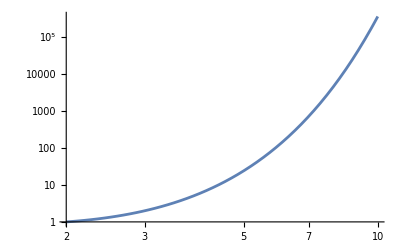

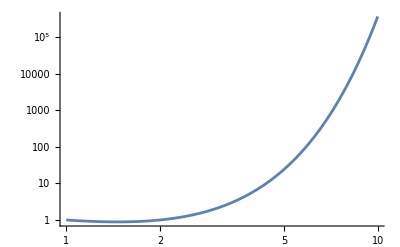

```mathematica
LogLogPlot[Gamma[x],{x,2,10}]
LogLogPlot[Gamma[x],{x,1,10}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*x= κperp0 + κpar0*)
kappapar0=1.01;
Manipulate[Plot[δ^x*(1-δ)^(-x-0.5-kappapar0),{x,1.01,300},PlotLabel->"κpar0=0.501, δ=" + δ,Frame->True,FrameLabel->{"x=κ_(⊥ 0)","(1-δ)^(-x - 1.01)"},ScalingFunctions->{"Log10","Linear"}],{δ,-10,10}]
```

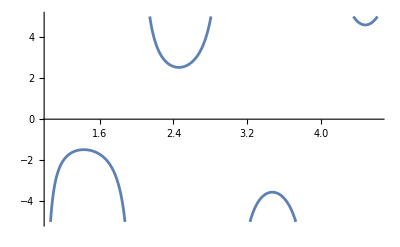

```mathematica
Plot[(Csc[Pi*x]*Gamma[x+1.01])/(Gamma[x]*Gamma[1.01]),{x,1,10},PlotRange->{All,{-5,5}}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*x= κperp0 + κpar0*)
kappapar0=10.01;
Manipulate[Plot[((Csc[Pi*x]*Gamma[x+0.5+kappapar0])/(Gamma[x]*Gamma[0.5+kappapar0]))*δ^x*(1-δ)^(-x-0.5-kappapar0),{x,1.01,300},PlotLabel->"κpar0=," <> ToString[kappapar0]<> ", δ=" + ToString[δ],Frame->True,FrameLabel->{"x=κ_(⊥ 0)","(1-δ)^(-x - 1.01)"},ScalingFunctions->{"Log10","Log10"}],{δ,0,0.99}]
```

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 
             -56            -260
   4.26631 10    -5.23693 10
     is too small to represent as a normalized machine number; precision may
     be lost.

General::munfl: 
             -63            -300
   6.41651 10    -3.11945 10
     is too small to represent as a normalized machine number; precision may
     be lost.

General::munfl: 
                       -347
   1. 5.098961685424 10     is too small to represent as a normalized machine
     number; precision may be lost.

General::stop: Further output of General::munfl
     will be suppressed during this calculation.

General::munfl: 
             -56            -260
   4.26631 10    -5.23693 10
     is too small to represent as a normalized machine number; precision may
     be lost.

General::munfl: 
             -63            -300
   6.41651 10    -3.11945 10
     is too small to represent as a normalized machine number; precision may
     be lost.

General::munfl: 
                       -347
   1. 5.098961685424 10     is too small to represent as a normalized machine
     number; precision may be lost.

General::stop: Further output of General::munfl
     will be suppressed during this calculation.

General::munfl: 4.26631×10^-56 (-5.23693×10^-260) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41651×10^-63 (-3.11945×10^-300) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 5.098961685424×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
y1[η_,z_]:=Series[Series[(1/η)*Exp[z/η]*ExpIntegralE[1/η+1,z/η],{z,0,1},Assumptions->{0<=η<1}],{η,0,1},Assumptions->{z>=0}];

y2[η_,z_]:=Series[(1/η)*Exp[z/η]*ExpIntegralE[1/η+1,z/η],{z,0,1},{η,0,1},Assumptions->{0<=η<1,z>=0}];

y3[η_,z_]:=Series[(1/η)*Exp[z/η]*ExpIntegralE[1/η+1,z/η],{η,0,1},{z,0,1},Assumptions->{0<=η<1,z>=0}];

FullSimplify[y1[η,z],{z>=0,0<=η<1}]
FullSimplify[y2[η,z],{z>=0,0<=η<1}]
FullSimplify[y3[η,z],{z>=0,0<=η<1}]
```

(1+(-1-η+O[η]^2) z+O[z]^2)+z^(1/η+O[η]^2) (ⅇ^((1-Log[η])/η+O[η]^0) η^(1/η) Csc[π/η+O[η]^3] (-(√η)/2+O[η]^(5/2))+ⅇ^((1-Log[η])/η+O[η]^0) η^(1/η) Csc[π/η+O[η]^3] (-(√η)/2+O[η]^(5/2)) z+O[z]^2)

(1+(-1-η+O[η]^2) z+O[z]^2)+z^(1/η+O[η]^2) (ⅇ^(1/η+O[η]^0) Csc[π/η] (-√(π/2) √η+O[η]^(3/2))+ⅇ^(1/η+O[η]^0) Csc[π/η] (-√(π/2) √η+O[η]^(3/2)) z+O[z]^2)

ⅇ^((z+O[z]^2)/η+O[η]^2) (((1+O[η]^3)+(-1/η-1-η+O[η]^2) z+O[z]^2)+(z/η)^(1/η) Gamma[-1/η] (1/η+O[η]^2))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

FullSimplify[z^(1/η),{z>=0,0<=η<1}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

κ0=1.01;
κ1=1.51;
κ2=2.;
κ3=10.;
κ4=100.;
κ5=300.;

ff[z_,κ_]:=κ*Exp[κ*z]*ExpIntegralE[κ+1,κ*z];
(*η=1/κ*)
fasmall1[z_,κ_]:=1+ (-1-1/κ)*z+z^κ*(Exp[(1-Log[1/κ])/(1/κ)]*(1/κ)^κ Csc[Pi*κ]*((-√(1/κ))/2)(1+z))
fasmall2[z_,κ_]:=1+ (-1-1/κ)*z+z^κ*(Exp[(1-Log[1/κ])/(1/κ)]*Csc[Pi*κ]*(-√(π/2) √(1/κ))(1+z))
fasmall3[z_,κ_]:=Exp[κ*z]*(1+(-κ-1-1/κ)*z+(z*κ)^κ Gamma[-κ] *κ)
p3=Manipulate[Plot[ff[z,κ],{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Exact "},PlotRange->All,PlotLabel->κ],{κ,15,1000}]

zmin = 0;
zmax = 10;
p3=Manipulate[Plot[fasmall1[z,κ],{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)"," Approx"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]
p33=Manipulate[Plot[fasmall2[z,κ],{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)"," Approx"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]

p333=Manipulate[Plot[fasmall3[z,κ],{z,zmin,zmax},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)"," Approx"},PlotRange->All,PlotLabel->κ],{κ,15,1000}]


p3=Manipulate[Plot[fasmall1[z,κ]/ff[z,κ],{z,0,1},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Exact "},PlotRange->All,PlotLabel->κ,PlotRange->{All,{0,2}}],{κ,15,1000}]
p3=Manipulate[Plot[fasmall2[z,κ]/ff[z,κ],{z,0,1},Frame->True,FrameLabel->{"z=A_0(B/B_0-1)","Exact "},PlotRange->All,PlotLabel->κ,PlotRange->{All,{0,2}}],{κ,15,1000}]
```

Plot::plln: Limiting value zmin in {z, zmin, zmax}
     is not a machine-sized real number.

Plot::plln: Limiting value zmin in {z,zmin,zmax} is not a machine-sized real number.

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κ>3/2,x>=0};
FullSimplify[κ*Integrate[(1-t)^(2*κ-1/2)*(1-t*(1-x))^(-κ-1/2),{t,0,1},Assumptions->assumps]]
```

κ Gamma[1/2+2 κ] Hypergeometric2F1Regularized[1,1/2+κ,3/2+2 κ,1-x]